# Discontinuous Galerkin

## Modal DG

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

## Initialize Symbols & Notation

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Change Notebook to it’s original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

#### Load Notation package and create symbols

```mathematica
Needs["Notation`"]
```

```mathematica
Symbolize[Subscript[u, j-1/2]^+];Symbolize[Subscript[u, j-1/2]^-];Symbolize[Subscript[f̂, j-1/2]];
```

```mathematica
Symbolize[Subscript[u, j+1/2]^-];Symbolize[Subscript[u, j+1/2]^+];Symbolize[Subscript[f̂, j+1/2]];
```

```mathematica
Symbolize[u^+];Symbolize[u^-];
```

## Discontinuous Galerking Procedure

### Building the Domain

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nf = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Therefore the Jacobian metric between this two elements is given by,

```mathematica
J = Subscript[h, j]/2;
```

Now, let us define solution points, ξ_k, inside the standar element:
Lets define a polynomial of degree K=3 on either Legendre / Lobatto points,

```mathematica
K=3;
```

#### Legendre Polynomials

Generating up to 4th degree Legendre Polynomials.

```mathematica
legendreP = Table[LegendreP[i,ξ],{i,0,5}];
```

```mathematica
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}
```

{1,ξ,1/2 (-1+3 ξ^2),1/2 (-3 ξ+5 ξ^3),1/8 (3-30 ξ^2+35 ξ^4),1/8 (15 ξ-70 ξ^3+63 ξ^5)}

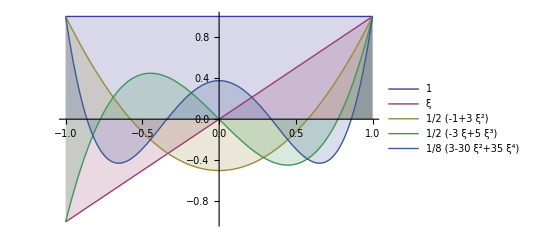

```mathematica
Plot[Evaluate[Most[legendreP]],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

Legendre Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[p, 4]==0,ξ][[All,2]],Greater]
```

{-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}

```mathematica
weights={1/36 (18-√30),1/36 (18+√30),1/36 (18+√30),1/36 (18-√30)};
```

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,5}] //Simplify;
```

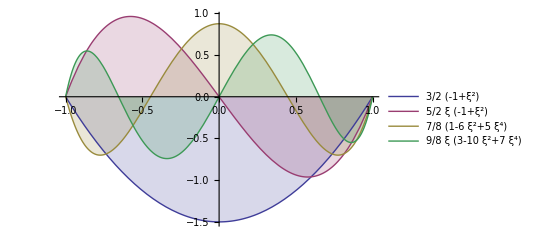

```mathematica
Plot[Evaluate[lobatto],{ξ,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+ξ^2)
5/2 ξ (-1+ξ^2)
7/8 (1-6 ξ^2+5 ξ^4)
9/8 ξ (3-10 ξ^2+7 ξ^4)

Lobatto Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 3]==0,ξ][[All,2]],Greater]
```

{-1,-1/(√5),1/(√5),1}

```mathematica
weights={1/6,5/6,5/6,1/6}
```

{1/6,5/6,5/6,1/6}

I, personally, prefer to call the abscissas ‘standard solution points’ or simply ‘solution points’. I will also  referer to all the points inside the domain as my ‘global nodes coordinates’.

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
```

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ J ×abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0. | 0.0276393 | 0.0723607 | 0.1
0.1 | 0.127639 | 0.172361 | 0.2
0.2 | 0.227639 | 0.272361 | 0.3
0.3 | 0.327639 | 0.372361 | 0.4
0.4 | 0.427639 | 0.472361 | 0.5
0.5 | 0.527639 | 0.572361 | 0.6
0.6 | 0.627639 | 0.672361 | 0.7
0.7 | 0.727639 | 0.772361 | 0.8
0.8 | 0.827639 | 0.872361 | 0.9
0.9 | 0.927639 | 0.972361 | 1.

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u0(x) = 0.5 +sin(2πx), therefore

```mathematica
Table[Subscript[x, j,k]= Subscript[x, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

```mathematica
u0[x_]:=0.5+Sin[2 π x]; (* or *)
u0[x_]:= Piecewise[{{2,x<=0.45},{1,x>0.45}}];
Subscript[u, 𝒟] = Table[u0[Subscript[x, j,k]],{j,1,10},{k,1,4}];
Subscript[u, 𝒟]//TableForm
```

2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=4 and k=1, we should get

```mathematica
Subscript[u, 4,1]
```

2

#### Continuous Case

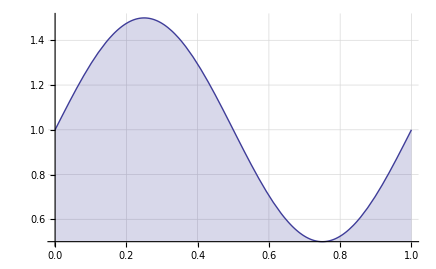

```mathematica
u[x_,t_]:= 0.5(2+Sin[2π x]);
sin =Plot[u[x,t],{x,0,1},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

#### Discontinuous Case

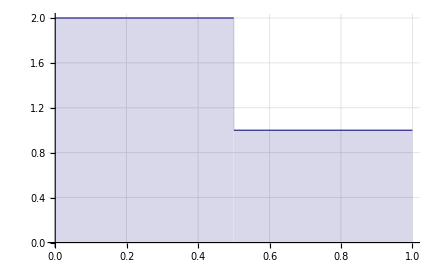

```mathematica
u[x_,t_]:= Piecewise[{{2,x<0.5},{1,x>=0.5}}]
Plot[u[x,t],{x,0,1},PlotRange->{0,2},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Filling->Axis]
```

Assume t = 0. Evaluate u[x, t] at discrete value points,

### Select a weighting function

Let us select Legendre Polynomials as our weighting function as a function of ξ ∈ [-1,1],

```mathematica
Table[Subscript[v, l]= LegendreP[l,x],{l,0,6}];
```

```mathematica
{Subscript[v, 0],Subscript[v, 1],Subscript[v, 2],Subscript[v, 3],Subscript[v, 4]}
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4)}

### Compute Degrees of freedom u_j^(l)

For u_j element using the continuous function u(x,t). If we define the degrees of freedom as:

u_j^(l) = u_j^(l)[t] = 1/Δx_j^(l+1)∫_I_j u[x,t] v_l^(j)[x]ⅆx, for l = 1,...,k

```mathematica
Subscript[u, j]^(l)=1/Δx^(l+1)∫_Subscript[x, j-3/2]^Subscript[x, j-1/2] Subscript[u, j,k] Subscript[v, l] ⅆx
```